```mathematica
F[q_] := 2-3 Sqrt[Pi] q Exp[q^2] Erfc[q]
 h11[q_,g11_, g12_, g22_, D11_, l11_, n1_] := n1 (g11/(Sqrt[2 Pi] l11)+D11 F[q l11/Sqrt[2]])
h12 [q_, g11_, g12_, g22_, D11_, l12_, n2_] := n2 (g12/(Sqrt[2 Pi] l12))
h21 [q_, g11_, g12_, g22_, D11_, l12_, n1_] := n1 (g12/(Sqrt[2 Pi] l12))
h22 [q_, g11_, g12_, g22_, D11_, l22_, n2_] := n2 (g22/(Sqrt[2 Pi] l22))
w1[q_, g11_, g12_, g22_, D11_, l11_, n1_] := Sqrt[q^2/(2 M1) (q^2/(2M1)+2 h11[q, g11, g12, g22, D11, l11, n1])]
w2[q_, g11_, g12_, g22_, D11_, l22_, n2_] :=  Sqrt[q^2/(2 M2) (q^2/(2M2)+2 h22[q, g11, g12, g22, D11, l22, n2])]
w2sound[q_, g11_, g12_, g22_, D11_, l22_, n2_] := Sqrt[q^2/(2 M2) 2 h22[q, g11, g12, g22, D11, l22, n2]]
wp[q_, g11_, g12_, g22_, D11_, l11_, l12_, l22_, n1_, n2_] := Sqrt[1/2 (w1[q, g11, g12, g22, D11, l11, n1]^2+w2[q, g11, g12, g22, D11, l22, n2]^2+Sqrt[(w1[q, g11, g12, g22, D11, l11, n1]^2-w2[q, g11, g12, g22, D11, l22, n2]^2)^2+4 q^4/(M1 M2) h12[q, g11, g12, g22, D11, l12, n2] h21[q, g11, g12, g22, D11, l12, n1]])]
wm[q_, g11_, g12_, g22_, D11_, l11_, l12_, l22_, n1_, n2_] := Sqrt[1/2 (w1[q, g11, g12, g22, D11, l11, n1]^2+w2[q, g11, g12, g22, D11, l22, n2]^2-Sqrt[(w1[q, g11, g12, g22, D11, l11, n1]^2-w2[q, g11, g12, g22, D11, l22, n2]^2)^2+4 q^4/(M1 M2) h12[q, g11, g12, g22, D11, l12, n2] h21[q, g11, g12, g22, D11, l12, n1]])]
```

```mathematica
h11int[q_] :=  n1 (g11/(Sqrt[2 Pi] l11)+ D11 l11/Sqrt[2 Pi] NIntegrate[Exp[-l11^2/2 (x^2)] (3 x^2/(x^2+q^2)-1),{x,-Infinity,Infinity} ])
```

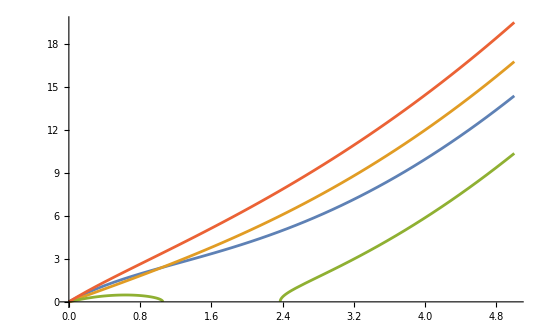

```mathematica
M1 = 1;
hbar = 1;
M2 = 1;
lz1 = 1;
lz2 = lz1 Sqrt[M1/M2];
l11 = lz1;
l12 = Sqrt[(lz1^2+lz2^2)/2];
l22 = lz2;
n1 = n2 = 1;
a11 = a22 = 1;
a12 = 1.05;
b11 = 2/3;
g11 = 4 Pi hbar^2 a11/M1;
g12 = 2 Pi hbar^2 a12/(M1 M2/(M1+M2));
g22 = 4 Pi hbar^2 a22/M2;
D11 = 2 Sqrt[2 Pi] hbar^2 b11/(M1 l11);
Plot[{w1[q], w2[q], wm[q], wp[q]},{q,0,5}]
```

{{1,1},{2,0.99},{5,0.92},{10,0.84},{20,0.75},{24,0.73}}

{{1,1.5},{2,1.4},{5,1.2},{10,1.15},{20,0.99},{24,0.95}}

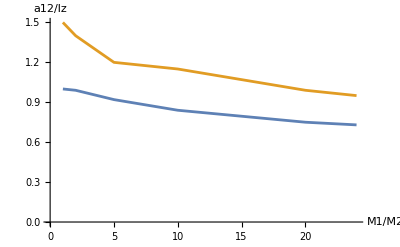

```mathematica
ls = {{1,1},{2,0.99},{5,0.92},{10,0.84},{20,0.75},{24,0.73}}
rs = {{1,1.5},{2,1.4},{5,1.2},{10,1.15},{20,0.99},{24,0.95}}
ListLinePlot[{ls,rs} ,AxesLabel-> {"M1/M2", "a12/lz"}]
```

```mathematica
5.29 10^-11 /Sqrt[(1.05 10^-34)/(150 166 1.66 10^-27 )]
```

0.0000331906

```mathematica
0.002157387195134098/0.00003319057223283227
```

65.

```mathematica
M1 = 1;
hbar = 1;
M2 = 1/2;
lz1 = 1;
lz2 = lz1 (M1/M2)^(1/4);
l11 = lz1;
l12 = Sqrt[(lz1^2+lz2^2)/2];
l22 = lz2;
n1 = n2 = 600;
a11 =65 (0.00003319057223283227);
a22 = 65 (0.00003319057223283227);
a12 = 60(0.00003319057223283227);
b11 =64 (0.00003319057223283227);
g11 = 4 Pi hbar^2 a11/M1;
g12 = 2 Pi hbar^2 a12/(M1 M2/(M1+M2));
g22 = 4 Pi hbar^2 a22/M2;
qt = Sqrt[2 2 M2 n2 g22/(Sqrt[2 Pi] l22) ];
D11 = 2Sqrt[2 Pi] hbar^2 b11/(M1 l11);
Manipulate[Plot[{ w1[q,g11, g12, g22, D11], w2[q,g11, g12, g22, D11], wp[q,g11, g12, g22, D11], wm[q,g11, g12, g22, D11]},{q,0,10}, PlotLegends->{"w1","w2", "w+", "w-"}],{g11, 0.1, 2}, {g12, 0, 5}, {g22, 0.1,2}, {D11, 0, 2}]
```

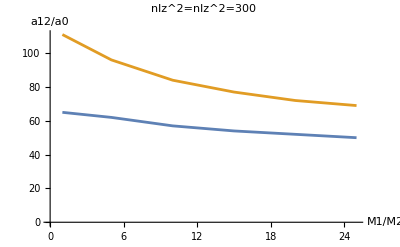

```mathematica
ls = {{1,65},{5,62},{10,57},{15,54},{20,52},{25,50}};
rs= {{1,111},{5,96},{10,84},{15,77},{20,72},{25,69}};
ListLinePlot[{ls,rs} ,AxesLabel-> {"M1/M2", "a12/a0"},PlotLabel->"nlz^2=nlz^2=300"]
```

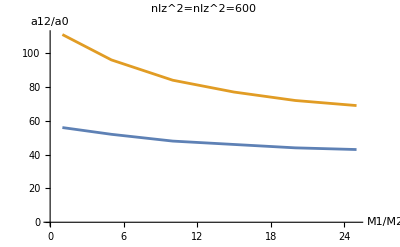

```mathematica
ls = {{1,56},{5,52},{10,48},{15,46},{20,44},{25,43}};
rs= {{1,111},{5,96},{10,84},{15,77},{20,72},{25,69}};
ListLinePlot[{ls,rs} ,AxesLabel-> {"M1/M2", "a12/a0"},PlotLabel->"nlz^2=nlz^2=600"]
```

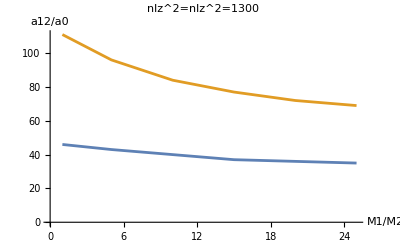

```mathematica
ls = {{1,46},{5,43},{10,40},{15,37},{20,36},{25,35}};
rs= {{1,111},{5,96},{10,84},{15,77},{20,72},{25,69}};
ListLinePlot[{ls,rs} ,AxesLabel-> {"M1/M2", "a12/a0"},PlotLabel->"nlz^2=nlz^2=1300"]
```

```mathematica
ls3 = {{1,65},{5,62},{10,57},{15,54},{20,52},{25,50}};
rs3= {{1,111},{5,96},{10,84},{15,77},{20,72},{25,69}};
ls6 = {{1,56},{5,52},{10,48},{15,46},{20,44},{25,43}};
rs6= {{1,111},{5,96},{10,84},{15,77},{20,72},{25,69}};
ls13= {{1,46},{5,43},{10,40},{15,37},{20,36},{25,35}};
rs13= {{1,111},{5,96},{10,84},{15,77},{20,72},{25,69}};
ListLinePlot[{ls3, ls6, ls13, rs13}, PlotLabels-> {"nl_z^2=300", "nl_z^2=600", "nl_z^2=1300", "IMT"} ,FrameLabel->{"M_1/M_2", "a_12/a_0"}, Frame->True, LabelStyle->Directive[FontFamily->"Times"]]
```

-Graphics-

```mathematica
M1 = 1;
hbar = 1;
M2 = 1/24;
α2 = 270/166;
lz1 = 1;
lz2 = lz1 (M1/(M2 α2) )^(1/4);
l11 = lz1;
l12 = Sqrt[(lz1^2+lz2^2)/2];
l22 = lz2;
n1 = 1300;
n2 = 1300;
Manipulate[Plot[{ w1[q,4 Pi hbar^2 a11 0.00003319057223283227/M1, 2 Pi hbar^2 a12 0.00003319057223283227/(M1 M2/(M1+M2)), 4 Pi hbar^2 a22 0.00003319057223283227/M2, 2Sqrt[2 Pi] hbar^2 b11 0.00003319057223283227/(M1 l11), l11, n1], w2[q,4 Pi hbar^2 a11 0.00003319057223283227/M1, 2 Pi hbar^2 a12 0.00003319057223283227/(M1 M2/(M1+M2)), 4 Pi hbar^2 a22 0.00003319057223283227/M2, 2Sqrt[2 Pi] hbar^2 b11 0.00003319057223283227/(M1 l11), l22, n2], wp[q,4 Pi hbar^2 a11 0.00003319057223283227/M1, 2 Pi hbar^2 a12 0.00003319057223283227/(M1 M2/(M1+M2)), 4 Pi hbar^2 a22 0.00003319057223283227/M2, 2Sqrt[2 Pi] hbar^2 b11 0.00003319057223283227/(M1 l11), l11, l12, l22, n1, n2], wm[q,4 Pi hbar^2 a11 0.00003319057223283227/M1, 2 Pi hbar^2 a12 0.00003319057223283227/(M1 M2/(M1+M2)), 4 Pi hbar^2 a22 0.00003319057223283227/M2, 2Sqrt[2 Pi] hbar^2 b11 0.00003319057223283227/(M1 l11), l11, l12, l22, n1, n2], w2sound[q,4 Pi hbar^2 a11 0.00003319057223283227/M1, 2 Pi hbar^2 a12 0.00003319057223283227/(M1 M2/(M1+M2)), 4 Pi hbar^2 a22 0.00003319057223283227/M2, 2Sqrt[2 Pi] hbar^2 b11 0.00003319057223283227/(M1 l11), l22, n2] },{q,0,10}, PlotLegends->{"w1","w2", "w+", "w-"}, PlotRange->{0,100}],{a11, 65}, {a12, 0, 120}, {a22, 10,80}, {b11, 64}]
```

```mathematica
ls3 = {{1,1},{5,0.6106197248236792},{10,0.42988433821977007},{15,0.33958654835390933},{20,0.2834467120181405},{25,0.24999999999999994}};
rs3= {{1,0.34291047804561303},{5,0.254689911265432},{10,0.1979441914506849},{15,0.1670154115365154},{20,0.14784720472551155},{25,0.13127494223902544}};
ls6 = {{1,1.3472576530612244},{5,0.8680555555555552},{10,0.6062040863177225},{15,0.46797465737240057},{20,0.3958883829013699},{25,0.33802055164954026}};
ls13= {{1,1.9966918714555764},{5,1.269454960639384},{10,0.8729338842975207},{15,0.723326789627465},{20,0.5913888189020462},{25,0.510204081632653}};
Show[ListLinePlot[{ls3, ls6, ls13, rs3}, PlotLabels-> {"nl_z^2=300", "nl_z^2=600", "nl_z^2=1300", "IMT"} ,FrameLabel->{"M_1/M_2", "g_11g_22/(g_12)^2"}, Frame->True, LabelStyle->Directive[FontFamily->"Times"]]]
```

-Graphics-

```mathematica
110-65
```

45

```mathematica
Integrate[Exp[-L^2/2 (x^2)] (3 x^2/(x^2+z^2)-1),{x,-Infinity,Infinity},Assumptions-> Element[L, NonNegativeReals] && Element[z, NonNegativeReals] ]
```

ConditionalExpression[(2 √(2 π))/L-3 ⅇ^((L^2 z^2)/2) π z Erfc[(L z)/(√2)], z>0]

```mathematica
Integrate[ⅇ^(-1/2 L^2 y^2) ((2 √(2 π))/L-(3 ⅇ^(1/2 L^2 (y^2+z^2)) π Erfc[L/(√2 √(1/(y^2+z^2)))])/(√(1/(y^2+z^2)))),{y,-Infinity,Infinity}]
```

$Aborted

```mathematica
Integrate[1/(2 Pi) Exp[-1/4 k^2 l^2 + I k z],{k,-Infinity,Infinity}]
```

ConditionalExpression[(ⅇ^(-z^2/l^2))/(√(l^2) √π), Re[l^2]>0]

```mathematica
Integrate[ 1/(2 Pi) Exp[-L^2/2 (x^2)] (3 x^2/(x^2+q^2)-1),{x,-Infinity, Infinity},Assumptions-> Element[q,NonNegativeReals] && Element[L, NonNegativeReals]]
```

ConditionalExpression[(√(2/π))/L-3/2 ⅇ^((L^2 q^2)/2) q Erfc[(L q)/(√2)], q>0]

```mathematica
FullSimplify[(1/(L √(2 π))-3/4 ⅇ^((L^2 q^2)/2) q Erfc[(L q)/(√2)]  )(2 Pi h^2/mjk bjk)]
```

(2 bjk h^2 π (1/(L √(2 π))-3/4 ⅇ^((L^2 q^2)/2) q Erfc[(L q)/(√2)]))/mjk

```mathematica
FullSimplify[(2-3 Sqrt[Pi] q L /Sqrt[2] Exp[q^2 L^2/2] Erfc[q L/Sqrt[2]]) 2 Sqrt[2 Pi] h^2 bjk/(Mjk L)]
```

(2 bjk h^2 (2 √(2 π)-3 ⅇ^((L^2 q^2)/2) L π q Erfc[(L q)/(√2)]))/(L Mjk)

```mathematica
M1 = 1;
hbar = 1;
M2 = 1/10;
lz1 = 1;
lz2 = lz1 Sqrt[M1/M2];
l11 = lz1;
l12 = Sqrt[(lz1^2+lz2^2)/2];
l22 = lz2;
n1 = n2 = 1300;
a11 = a22 =65 (0.00003319057223283227);
a12 = 0(0.00003319057223283227);
b11 =64 (0.00003319057223283227); 
NSolve[ w1[q  ,4 Pi hbar^2 a11 0.00003319057223283227/M1, 2 Pi hbar^2 a12 0.00003319057223283227/(M1 M2/(M1+M2)), 4 Pi hbar^2 a22 0.00003319057223283227/M2, 2Sqrt[2 Pi] hbar^2 b11 0.00003319057223283227/(M1 l11)] ==  w2[q  ,4 Pi hbar^2 a11 0.00003319057223283227/M1, 2 Pi hbar^2 a12 0.00003319057223283227/(M1 M2/(M1+M2)), 4 Pi hbar^2 a22 0.00003319057223283227/M2, 2Sqrt[2 Pi] hbar^2 b11 0.00003319057223283227/(M1 l11)], {q} ]
```

{{q→0.}}

```mathematica
Series[Sqrt[1/2((ω1^2+ω2^2)- Sqrt[(ω1^2-ω2^2)^2+4 q^4/M1M2 h12q^2])], {h12q,0,4} , Assumptions-> {ω1>0, ω2 > 0, ω2>ω1}]
```

ω1+(q^4 h12q^2)/(2 M1M2 ω1 (ω1^2-ω2^2))-((q^8 (5 ω1^2-ω2^2)) h12q^4)/(8 (M1M2^2 ω1^3 (ω1^2-ω2^2)^3))+O[h12q]^5

```mathematica
Integrate[(3 kz^2/(kz^2+kr^2)-1) Exp[-1/2 kz^2 (ljk^2)], {kz, -Infinity, Infinity}, Assumptions-> kr >0 ]
```

ConditionalExpression[(2 √(2 π))/(√(ljk^2))-3 ⅇ^((kr^2 ljk^2)/2) kr π Erfc[(kr √(ljk^2))/(√2)], Re[ljk^2]>0]

```mathematica
(2 √(2 π))/(√(ljk^2))-3 ⅇ^((kr^2 ljk^2)/2) kr π Erfc[(kr √(ljk^2))/(√2)] /. {kr -> q Sqrt[2]/ljk}
```

(2 √(2 π))/(√(ljk^2))-(3 √2 ⅇ^(q^2) π q Erfc[(√(ljk^2) q)/ljk])/ljk

```mathematica
Series[ F[q^2], {q, 0,8}, Assumptions->Element[q, Reals]]
```

2-3 √π q^2+6 q^4-3 √π q^6+4 q^8+O[q]^9

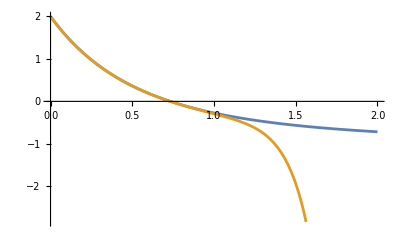

```mathematica
Plot[{F[q], 2-3 Sqrt[Pi] q Exp[q^2] (1-2/Sqrt[Pi] Sin[Sin[q]]) },{q,0,2}]
```

```mathematica
M[q_] :=(q^2+A+B (-1+3Exp[-q])) (q^2+D)
```

```mathematica
FullSimplify[M'[q]]
```

-3 B ⅇ^-q (D+(-2+q) q)+2 q (A-B+D+2 q^2)

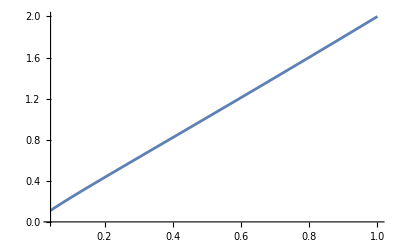

```mathematica
Plot[(1/x) /(1/x^2) (1+(1/x)^(1/2))/(1/x^(1/4)) ,{x,1/24,1}]
```

```mathematica
Simplify[1/((1/x) /(1/x^2) (1+(1/x)^(1/2))/(1/x^(1/4))), Assumptions->x>0]
```

1/((1+√x) x^(3/4))

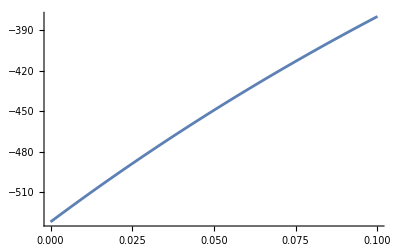

```mathematica
G[q_] := ( 100 (1 +   F[q])) (q^2+1)
Plot[G'[q], {q,0,0.1}]
```

```mathematica
4 n1 Sqrt[2 Pi] /l11 a11
4 n2 a22 /l11 Sqrt[2 Pi Sqrt[α2 M2/M1]]
```

28.1204

9.93303

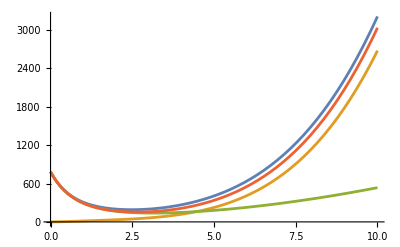

```mathematica
Plot[{(q^2/2+28 (1+0.9 F[q/Sqrt[2]]))(q^2/2+10),(q^2/2+28 (1+0.9 F[q/Sqrt[2]]))(q^2/2) , (q^2/2+28 (1+0.9 F[q/Sqrt[2]]))10 , (q^2/2+28 (1+0.9 F[q/Sqrt[2]]))10 + q^4/4  }, {q, 0, 10}]
```

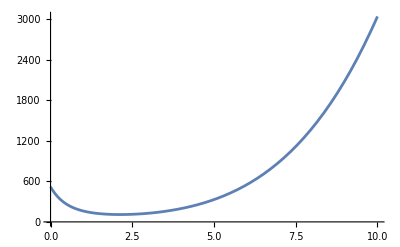

```mathematica
G[q_] := (q^2/2+20(1+ϵdd F[q]) ) 10 + q^4/4
Plot[G[q] /. ϵdd -> 0.8,{q,0,10}]
```